# Exponent analysis

## Preliminaries

### notebook save

```mathematica
maindir=SetDirectory[NotebookDirectory[]]
nbf=NotebookFileName[];
```

/storage/disqs/CCxD/Analysis_SS

### setting parameters

```mathematica
matrix = 0;
configs = 500000000;
iditer = 3;
zrange = 25;
bootstrapamt = 1;
bootstrapsets=10;
tippercentamt = 4;
cropamt = 8;
importrange = Table[i,{i,1,(rgsteps=3)}];
maxfitpointpushvalueindex=1;
maxfitpointrgstepindex=3;
project="CCGD";
zpushvalues = {0.02};
gdamt = 0;
strapplot=1;
```

## importing the data

```mathematica
datadir=maindir<>"/../"<>project<>"/data/";
SetDirectory[datadir];
filepath = datadir<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[iditer]<>"-"<>ToString[gdamt]<>"/push/BS";
```

```mathematica
import = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[matrix]<>"-"<>ToString[configs]<>"-"<>ToString[j]<>"/"<>ToString[k]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,1,bootstrapamt},{j,zpushvalues},{k,importrange}];
```

## doing the analysis

### determining the maximal-z positions

```mathematica
import[[1]][[1]][[1]]
transposed = Transpose[import,1<->4]
strapimportavg = Table[Total[transposed[[k]][[i]][[j]]]/bootstrapamt,{i,1,Length[zpushvalues]},{j,importrange},{k,1,Length[import[[1]][[1]][[1]]]}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,49802,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
 |  |  |  |

{{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},49965,{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}},{{{0.},{0.},{0.}}}}
 |  |  |  |

{{1}}
 |  |  |  |

```mathematica
toppercent = Table[RandomSample[Take[Ordering[import[[i]][[j]][[k]]],-(Length[import[[i]][[j]][[k]]]/(100/tippercentamt))]],{i,1,bootstrapamt},{j,1,Length[zpushvalues]},{k,importrange}];
totals = Table[Total[import[[i]][[j]][[k]]],{i,1,bootstrapamt},{j,1,Length[zpushvalues]},{k,importrange}];
tip = Table[{(l/1000)-(zrange + 0.0005),(import[[i]][[j]][[k]][[l]])*1000/totals[[i]][[j]][[k]]},{i,1,bootstrapamt},{j,1,Length[zpushvalues]},{k,importrange},{l,toppercent[[i]][[j]][[k]]}];
full = Table[{(l/1000)-(zrange + 0.0005),(import[[i]][[j]][[k]][[l]])*1000/totals[[i]][[j]][[k]]},{i,1,bootstrapamt},{j,1,Length[zpushvalues]},{k,importrange},{l,1000*(zrange-cropamt),Length[import[[1]][[1]][[1]]]}];
rescale = Table[Take[full[[i]][[j]][[k]],{1,Length[full[[i]][[j]][[k]]],50}],{i,1,bootstrapamt},{j,1,Length[zpushvalues]},{k,importrange}];
```

```mathematica
tipsubsets = Table[Take[tip[[i]][[j]][[k]],{(Length[tip[[i]][[j]][[k]]]/(bootstrapsets))*(l-1)+1,(l*Length[tip[[i]][[j]][[k]]])/(bootstrapsets)}],{i,1,bootstrapamt},{j,1,Length[zpushvalues]},{k,importrange},{l,1,bootstrapsets}];
```

```mathematica
straptoppercentavg = Table[RandomSample[Take[Ordering[strapimportavg[[i]][[j]]],-(Length[strapimportavg[[i]][[j]]]/(100/tippercentamt))]],{i,1,Length[zpushvalues]},{j,importrange}];
straptotalsavg = Table[Total[strapimportavg[[i]][[j]]],{i,1,Length[zpushvalues]},{j,importrange}];
straptipavg = Table[{(k/1000)-(zrange + 0.0005),(strapimportavg[[i]][[j]][[k]])*1000/straptotalsavg[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange},{k,straptoppercentavg[[i]][[j]]}];
strapfullavg = Table[{(k/1000)-(zrange + 0.0005),(strapimportavg[[i]][[j]][[k]])*1000/straptotalsavg[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange},{k,1000*(zrange-cropamt),Length[strapimportavg[[1]][[1]]]}];
straptipsubsetsavg = Table[Take[straptipavg[[i]][[j]],{(Length[straptipavg[[i]][[j]]]/(bootstrapsets))*(k-1)+1,(k*Length[straptipavg[[i]][[j]]])/(bootstrapsets)}],{i,1,Length[zpushvalues]},{j,importrange},{k,1,bootstrapsets}];
```

### Plotting Tip of Z dist

```mathematica
tipextrema = Table[{Min[straptipavg[[i]]],Max[straptipavg[[i]]]},{i,1,Length[zpushvalues]}];
fullextrema = Table[{Min[strapfullavg[[i]]],Max[strapfullavg[[i]]]},{i,1,Length[zpushvalues]}];
```

```mathematica
tipplot = Table[tipsubplot = {};For[j=1,j<=Length[importrange],j++,(
AppendTo[tipsubplot,ListPlot[straptipavg[[i]][[j]],Frame->True,PlotLabel->zpushvalues[[i]],LabelStyle->{FontSize->24}, FrameLabel->{"z","Q(z)"},PlotRange->{{tipextrema[[i]][[1]],tipextrema[[i]][[2]]},{0,Automatic}}, PlotStyle->RGBColor[j/Length[importrange],0.75,1-(j/Length[importrange])]]];
)];Show[tipsubplot],{i,1,Length[zpushvalues]}];
```

```mathematica
fullplot = Table[subplot = {};For[j=1,j<=Length[importrange],j++,(
AppendTo[subplot,ListPlot[strapfullavg[[i]][[j]],Frame->True,PlotLabel-> zpushvalues[[i]],LabelStyle->{FontSize->24},FrameLabel->{"z","Q(z)"}, PlotRange->{{-cropamt,zrange},All}, PlotStyle->RGBColor[j/Length[importrange],0.75,1-(j/Length[importrange])]]];
)];Show[subplot],{i,1,Length[zpushvalues]}];

(*GraphicsColumn[Table[ListPlot3D[full[[i]], AxesLabel->{"z","RG Step","Q(z)"}],{i,1,Length[zpushvalues]}]];*)
```

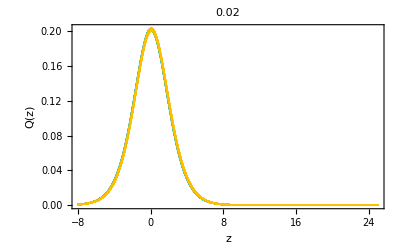

```mathematica
GraphicsColumn[fullplot]
```

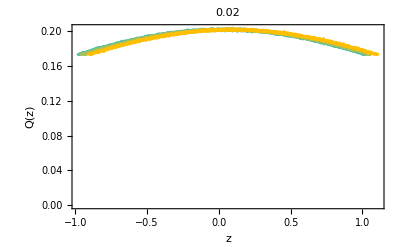

```mathematica
GraphicsColumn[tipplot]
```

#### 3D Plots

```mathematica
(*GraphicsColumn[Table[ListPlot3D[Flatten[threedfull[[i]],1]],{i,1,Length[zpushvalues]}]]*)
```

#### starting to fit gaussian to determine zmax and errors

```mathematica
startingvals = NonlinearModelFit[tip[[1]][[1]][[1]],a Exp[-(x-b)^2/(2*c^2)],{a,b,c},x][[1]][[2]];
errors = {};
zmax=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[tip[[k]][[i]][[j]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x][[1]][[2]];
Append[errors,fit["ParameterErrors"]];
lasta = a /. fit;lastb = b /. fit; lastc = c/. fit; lastb,{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
errors=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[tip[[k]][[i]][[j]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x];lasta = a /. fit[[1]][[2]];lastb = b /. fit[[1]][[2]]; lastc = c/. fit[[1]][[2]]; fit["ParameterConfidenceIntervals"][[2]],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
bootstraperrors=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[tipsubsets[[l]][[i]][[j]][[k]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x][[1]][[2]];lasta = a /. fit;lastb = b /. fit; lastc = c/. fit; lastb,{l,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange},{k,1,bootstrapsets}];
bootstraperrormin = Table[zmax[[k]][[i]][[j]]-Min[bootstraperrors[[k]][[i]][[j]]],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
bootstraperrormax = Table[Max[bootstraperrors[[k]][[i]][[j]]]-zmax[[k]][[i]][[j]],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
errorsmin = Table[zmax[[k]][[i]][[j]]-Min[errors[[k]][[i]][[j]]],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
errorsmax = Table[Max[errors[[k]][[i]][[j]]]-zmax[[k]][[i]][[j]],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];

startingvalsavgstrap = NonlinearModelFit[straptipavg[[1]][[1]],a Exp[-(x-b)^2/(2*c^2)],{a,b,c},x][[1]][[2]];
errorsavgstrap = {};
zmaxavgstrap=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[straptipavg[[i]][[j]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x][[1]][[2]];
Append[errors,fit["ParameterErrors"]];
lasta = a /. fit;lastb = b /. fit; lastc = c/. fit; lastb,{i,1,Length[zpushvalues]},{j,importrange}];
errorsavgstrap=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[straptipavg[[i]][[j]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x];lasta = a /. fit[[1]][[2]];lastb = b /. fit[[1]][[2]]; lastc = c/. fit[[1]][[2]]; fit["ParameterConfidenceIntervals"][[2]],{i,1,Length[zpushvalues]},{j,importrange}];
bootstraperrorsavgstrap=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[straptipsubsetsavg[[i]][[j]][[k]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x][[1]][[2]];lasta = a /. fit;lastb = b /. fit; lastc = c/. fit; lastb,{i,1,Length[zpushvalues]},{j,importrange},{k,1,bootstrapsets}];
bootstraperrorminavgstrap = Table[zmaxavgstrap[[i]][[j]]-Min[bootstraperrorsavgstrap[[i]][[j]]],{i,1,Length[zpushvalues]},{j,importrange}];
bootstraperrormaxavgstrap = Table[Max[bootstraperrorsavgstrap[[i]][[j]]]-zmaxavgstrap[[i]][[j]],{i,1,Length[zpushvalues]},{j,importrange}];
errorsminavgstrap = Table[zmaxavgstrap[[i]][[j]]-Min[errorsavgstrap[[i]][[j]]],{i,1,Length[zpushvalues]},{j,importrange}];
errorsmaxavgstrap = Table[Max[errorsavgstrap[[i]][[j]]]-zmaxavgstrap[[i]][[j]],{i,1,Length[zpushvalues]},{j,importrange}];

rayplotwithouterrorsavgstrap = Table[{zpushvalues[[i]],zmaxavgstrap[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange}];
```

### Calculating nu and accompanying errors

```mathematica
numain = Table[Log[2^j]/Log[zmax[[k]][[i]][[j]]/(zpushvalues[[i]])],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
numin = Table[Log[2^j]/Log[(zmax[[k]][[i]][[j]]-bootstraperrormin[[k]][[i]][[j]])/(zpushvalues[[i]])],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
numax = Table[Log[2^j]/Log[(zmax[[k]][[i]][[j]]+bootstraperrormax[[k]][[i]][[j]])/(zpushvalues[[i]])],{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
rayplot = Table[{zpushvalues[[i]],Around[zmax[[k]][[i]][[j]],{bootstraperrormin[[k]][[i]][[j]],bootstraperrormax[[k]][[i]][[j]]}]},{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
raymin = Transpose[Transpose[Table[{zpushvalues[[i]],zmax[[k]][[i]][[j]]-bootstraperrormin[[k]][[i]][[j]]},{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}],2<->3]];
raymax = Transpose[Transpose[Table[{zpushvalues[[i]],zmax[[k]][[i]][[j]]+bootstraperrormax[[k]][[i]][[j]]},{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}],2<->3]];
rayplotwithouterrors=Transpose[Transpose[Table[{zpushvalues[[i]],zmax[[k]][[i]][[j]]},{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}],2<->3]];
```

```mathematica
rayplotwithouterrors[[1]][[1]]
```

{{0.02,0.0234764}}

```mathematica
Transpose[Flatten[rayplot,1]]
```

{{{0.02,0.02350.00200.0024}},{{0.02,0.05490.00270.0028}},{{0.02,0.09610.00180.0029}}}

```mathematica
rayplotwithouterrors[[3]][[10]]
```

Part::partw: Part 10 of {{{0.02,0.0960609}}} does not exist.

{{{0.02,0.0960609}}}⟦10⟧

#### Plotting the critical exponents

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

General::stop: Further output of LinearModelFit::rank will be suppressed during this calculation.

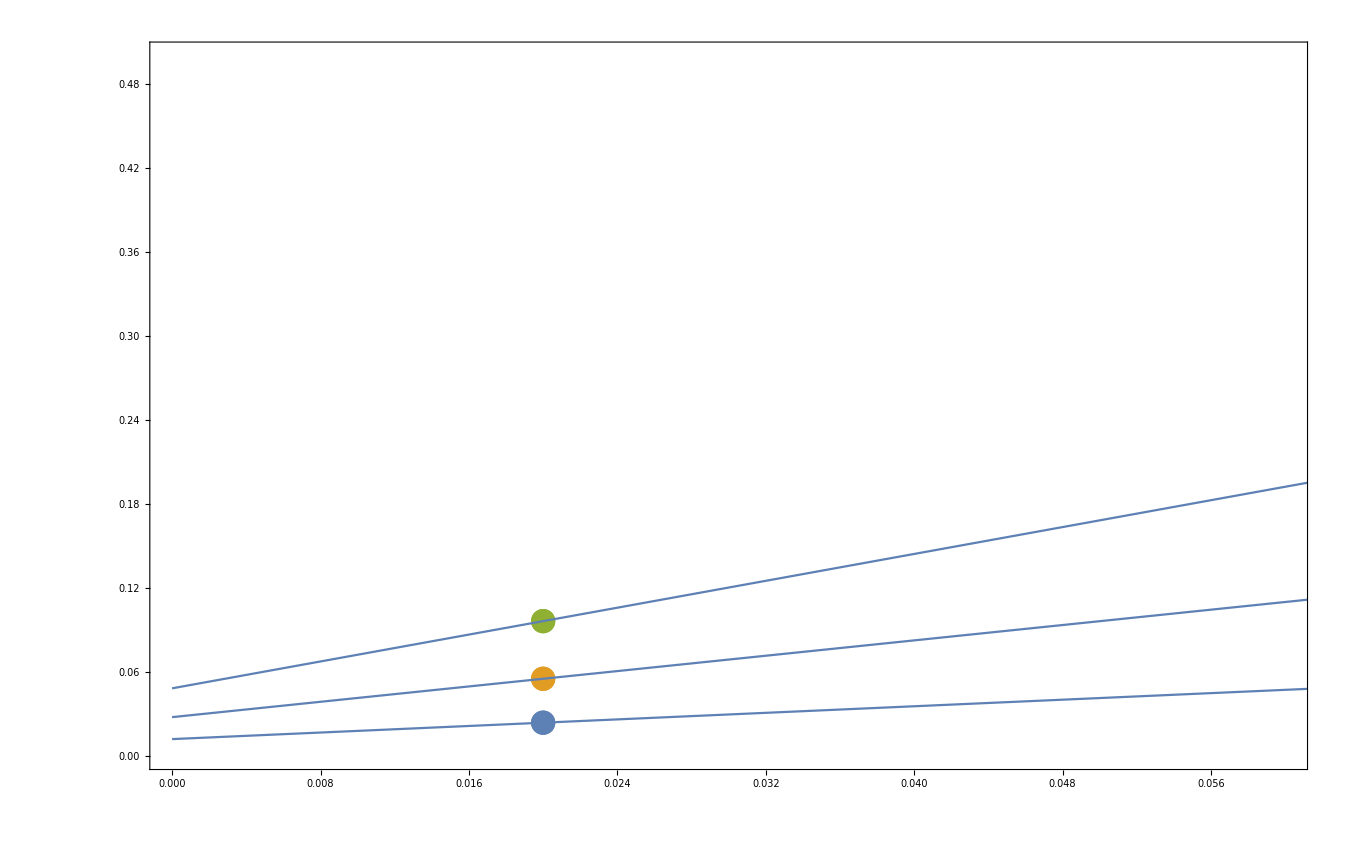

```mathematica
nuplot = Table[{2^j,Around[numain[[k]][[i]][[j]],{numain[[k]][[i]][[j]]-numin[[k]][[i]][[j]],numax[[k]][[i]][[j]]-numain[[k]][[i]][[j]]}]},{k,1,bootstrapamt},{i,1,Length[zpushvalues]},{j,importrange}];
GraphicsColumn[Table[nuplot[[k]][[i]],{k,1,bootstrapamt},{i,1,Length[zpushvalues]}]];
Show[ListPlot[Transpose[Flatten[rayplot,1]],PlotRange->{{0,0.06},{0,0.5}},Frame->True],Plot[Table[LinearModelFit[Take[rayplotwithouterrors[[i]][[j]],maxfitpointpushvalueindex],y,y][z],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}],{z,0,0.8},PlotRange->All]]
```

#### y intercepts of fitting lines without (0, 0)

```mathematica
yinterceptwo0 = Table[LinearModelFit[rayplotwithouterrors[[i]][[j]],x,x]["BestFitParameters"][[1]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

General::stop: Further output of LinearModelFit::rank will be suppressed during this calculation.

{{0.0117382},{0.027436},{0.0480304}}

```mathematica
gradients of fitting lines without (0,0)
```

```mathematica
gradientswo0 = Table[LinearModelFit[rayplotwithouterrors[[i]][[j]],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

General::stop: Further output of LinearModelFit::rank will be suppressed during this calculation.

{{0.58691},{1.3718},{2.40152}}

#### plot with (0,0)

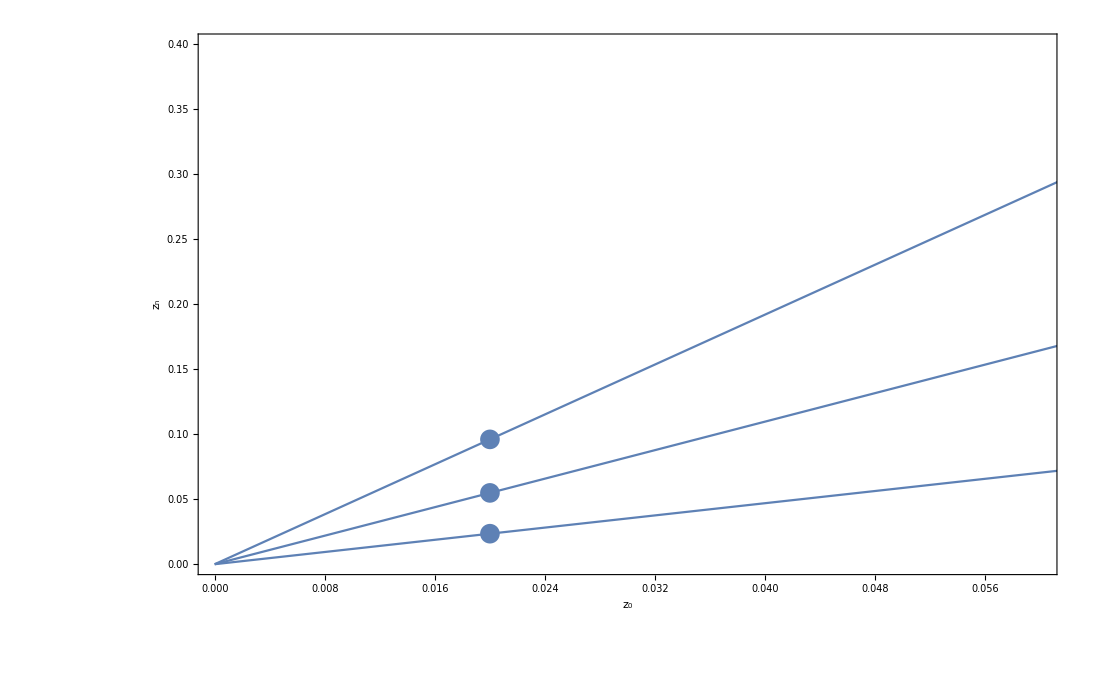

```mathematica
Show[ListPlot[Flatten[rayplot, 2],PlotRange->{{0,0.06},{0,0.4}},Frame->True,LabelStyle->{FontSize->24}, FrameLabel->{ToExpression["z_0",TeXForm,HoldForm],ToExpression["z_n",TeXForm,HoldForm]}],Plot[Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]][[j]],maxfitpointpushvalueindex],{0,0}],y,y][z],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}],{z,0,0.8},PlotRange->All,Frame->True]]
```

#### y intercepts of fitting lines with (0, 0)

```mathematica
yinterceptwithzero = Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]][[j]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[1]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
```

{{-1.49335×10^-18},{-9.8746×10^-19},{-1.8325×10^-18}}

#### gradients of fitting lines with (0, 0)

```mathematica
rayplotwithouterrorsavgstrap[[4]]
Prepend[Take[rayplotwithouterrorsavgstrap[[4]],maxfitpointpushvalueindex],{0,0}]
```

Part::partw: Part 4 of {{{0.02,0.0234764},{0.02,0.054872},{0.02,0.0960609}}} does not exist.

{{{0.02,0.0234764},{0.02,0.054872},{0.02,0.0960609}}}⟦4⟧

Part::partw: Part 4 of {{{0.02,0.0234764},{0.02,0.054872},{0.02,0.0960609}}} does not exist.

{{0,0},{{0.02,0.0234764},{0.02,0.054872},{0.02,0.0960609}}}

```mathematica
gradientsavgstrap = Table[LinearModelFit[Prepend[Take[Transpose[rayplotwithouterrorsavgstrap][[i]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex}]
```

{1.17382,2.7436,4.80304}

```mathematica
gradients = Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]][[j]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
gradientsmin = Table[LinearModelFit[Prepend[Take[raymin[[i]][[j]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
gradientsmax = Table[LinearModelFit[Prepend[Take[raymax[[i]][[j]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]

gradientserror = Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]][[j]],maxfitpointpushvalueindex],{0,0}],x,x]["ParameterErrors"][[2]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
```

{{1.17382},{2.7436},{4.80304}}

{{1.07341},{2.60752},{4.71081}}

{{1.29398},{2.88577},{4.94748}}

Power::infy: Infinite expression 1/0 encountered.

FittedModel::varnum: The estimated variance ComplexInfinity is not a positive number. Properties requiring division by the variance or standard error will not be computed.

Part::partw: Part 2 of Missing[] does not exist.

Power::infy: Infinite expression 1/0 encountered.

FittedModel::varnum: The estimated variance ComplexInfinity is not a positive number. Properties requiring division by the variance or standard error will not be computed.

Part::partw: Part 2 of Missing[] does not exist.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FittedModel::varnum: The estimated variance ComplexInfinity is not a positive number. Properties requiring division by the variance or standard error will not be computed.

General::stop: Further output of FittedModel::varnum will be suppressed during this calculation.

Part::partw: Part 2 of Missing[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{Missing[]⟦2⟧},{Missing[]⟦2⟧},{Missing[]⟦2⟧}}

#### nu calculated from the gradients

{{{2,4.35.1.6}},{{4,1.370.070.07}},{{8,1.3250.0170.025}}}

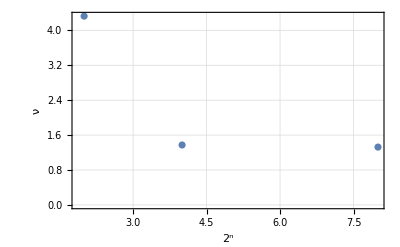

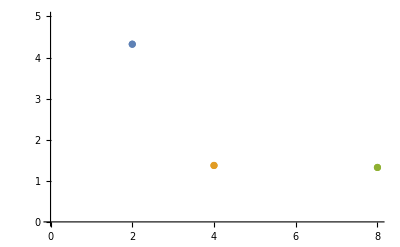

```mathematica
nufromgradientswitherror = Table[{2^i,Around[Log[2^i]/Log[gradients[[i]][[j]]],{Log[2^i]/Log[gradients[[i]][[j]]]-Log[2^i]/Log[gradientsmin[[i]][[j]]],Log[2^i]/Log[gradientsmax[[i]][[j]]]-Log[2^i]/Log[gradients[[i]][[j]]]}]},{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}]
nuvals = Table[Log[2^i]/Log[gradients[[i]][[j]]],{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}];
nuavg = Table[Total[nuvals[[i]]]/(bootstrapamt),{i,1,maxfitpointrgstepindex}];
numin = Table[nuavg[[i]]-Min[nuvals[[i]]],{i,1,maxfitpointrgstepindex}];
numax = Table[Max[nuvals[[i]]-nuavg[[i]]],{i,1,maxfitpointrgstepindex}];
nuwitherror = Table[{2^i,Around[nuavg[[i]],{numax[[i]],numin[[i]]}]},{i,1,maxfitpointrgstepindex}];
nufromgradientswithouterror = Table[{2^i,nuvals[[i]][[j]]},{i,1,maxfitpointrgstepindex},{j,1,bootstrapamt}];


ListPlot[nuwitherror,Frame->True,GridLines->Automatic, LabelStyle->{FontSize->24},FrameLabel->{ToExpression["2^n",TeXForm,HoldForm],ν}]
ListPlot[nufromgradientswithouterror,PlotRange->{{0,Automatic},{0,5}}]
```

{4.32506,1.37356,1.32512}

{{2,4.32506},{4,1.37356},{8,1.32512}}

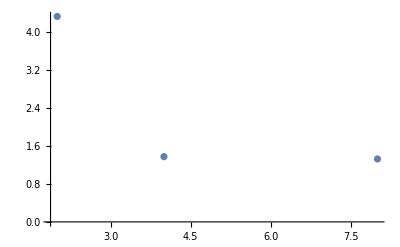

```mathematica
nuvalsavgstrap = Table[Log[2^i]/Log[gradientsavgstrap[[i]]],{i,1,maxfitpointrgstepindex}]
nufromgradientswithouterroravgstrap = Table[{2^i,nuvalsavgstrap[[i]]},{i,1,maxfitpointrgstepindex}]
ListPlot[nufromgradientswithouterroravgstrap]
```

## Saving

```mathematica
Directory[]
SetDirectory[maindir]
```

/storage/disqs/CCxD/CCGD/data

/storage/disqs/CCxD/Analysis_SS

```mathematica
nbf=NotebookFileName[]
NotebookSave[EvaluationNotebook[],"ExponentAnalysis-"<>ToString[configs]<>"-"<>ToString[matrix]<>"-"<>DateString[{"Day","-","Month","-","Year"}]<>".nb"]
NotebookSave[EvaluationNotebook[],nbf]
```

/storage/disqs/CCxD/Analysis_SS/ExponentAnalysis_SS-BS.nb